```mathematica
NN = 3;
mm  = 1.0;


M1 = mm ( ⅇ^(2 π ⅈ / NN) - 1. );
M2  = mm( ⅇ^(4 π ⅈ / NN) - 1. );
M = Abs[M1];
ϕ1[z_] := ⅇ^(M z)
χ[z_] := 1. + ϕ1[z] ϕ1[z]
f[z_] := (ϕ1[z])^2/χ[z]

eq1 := {  ψR'[z] - M f[z] ψR[z]   +  ⅈ ( M2* - M1* f[z]) ψL[z] == 0 };
eq2  := { ψL'[z] - M f[z] ψL[z]    -  ⅈ ( M2  -  M1 f[z] ) ψR[z] == 0 };
```

```mathematica
ψ = NDSolve[{ eq1, eq2, ψR[-10] == ⅇ^(Abs[M2] (-10.)), ψR[-11] ==ⅇ^(Abs[M2] (-11.))  }, {ψR, ψL},{z, -100, 100}]
Ψ = { ψR, ψL } /. ψ
ψR[z_] := Evaluate [ Ψ[[1]][[1]][z] ]
ψL[z_]  := Evaluate[ Ψ[[1]][[2]][z] ]
```

{{ψR→InterpolatingFunction[{{-100.,100.}},<>],ψL→InterpolatingFunction[{{-100.,100.}},<>]}}

{{InterpolatingFunction[{{-100.,100.}},<>],InterpolatingFunction[{{-100.,100.}},<>]}}

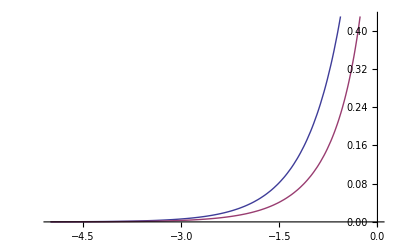

```mathematica
Plot[  {  Re[   ψR[z] ], Re[ ψL[z] ]  }, { z, -5, 0} ]
```

```mathematica
Plot[  {  Abs[  ψR[z]  ],     Abs[   ψL[z]  ]  }, { z, -90, 90} ]
```

-Graphics-